### Process

```mathematica
Clear[alfa,beta,n]
(*alfa<1/2, beta<1/2*)
PP={{1-alfa,alfa},{beta,1-beta}};
PP//MatrixForm
```

(1-alfa | alfa
beta | 1-beta)

```mathematica
Eigenvalues[PP]
Eigenvectors[PP]
```

{1,1-alfa-beta}

{{1,1},{-alfa/beta,1}}

```mathematica
lambda[1]=Eigenvalues[PP][[1]]
lambda[2]=Eigenvalues[PP][[2]]
u[1]=Eigenvectors[PP][[1]]
u[2]=Eigenvectors[PP][[2]]
```

1

1-alfa-beta

{1,1}

{-alfa/beta,1}

```mathematica
Umat={{u[1][[1]],u[2][[1]]},{u[1][[2]],u[2][[2]]}};
Vmat=Inverse[Umat]//Simplify;
LAMBDA={{lambda[1],0},{0,lambda[2]}};
LAMBDAn={{lambda[1]^n,0},{0,lambda[2]^n}};
Umat//MatrixForm
Vmat//MatrixForm
```

(1 | -alfa/beta
1 | 1)

(beta/(alfa+beta) | alfa/(alfa+beta)
-beta/(alfa+beta) | beta/(alfa+beta))

```mathematica
(*Check*)
PP-Umat.LAMBDA.Vmat//Simplify//PowerExpand//Simplify;
%//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
Umat.LAMBDAn.Vmat//Simplify//PowerExpand//Simplify;
%//MatrixForm
```

((alfa (1-alfa-beta)^n+beta)/(alfa+beta) | (alfa-alfa (1-alfa-beta)^n)/(alfa+beta)
(beta-(1-alfa-beta)^n beta)/(alfa+beta) | (alfa+(1-alfa-beta)^n beta)/(alfa+beta))

```mathematica
QQ=({{beta/(alfa+beta), alfa/(alfa+beta)}, {beta/(alfa+beta), alfa/(alfa+beta)}});
QQ//MatrixForm
```

(beta/(alfa+beta) | alfa/(alfa+beta)
beta/(alfa+beta) | alfa/(alfa+beta))

### Simulations

```mathematica
alfa=0.27;
beta=0.19;
nn=10000;
tauM=50;
```

```mathematica
lambda[2]
```

0.54

```mathematica
Umat//MatrixForm
Vmat//MatrixForm
```

(1 | -1.42105
1 | 1)

(0.413043 | 0.586957
-0.413043 | 0.413043)

(0.73 | 0.27
0.19 | 0.81)

TemporalData[…]

{10001,2}

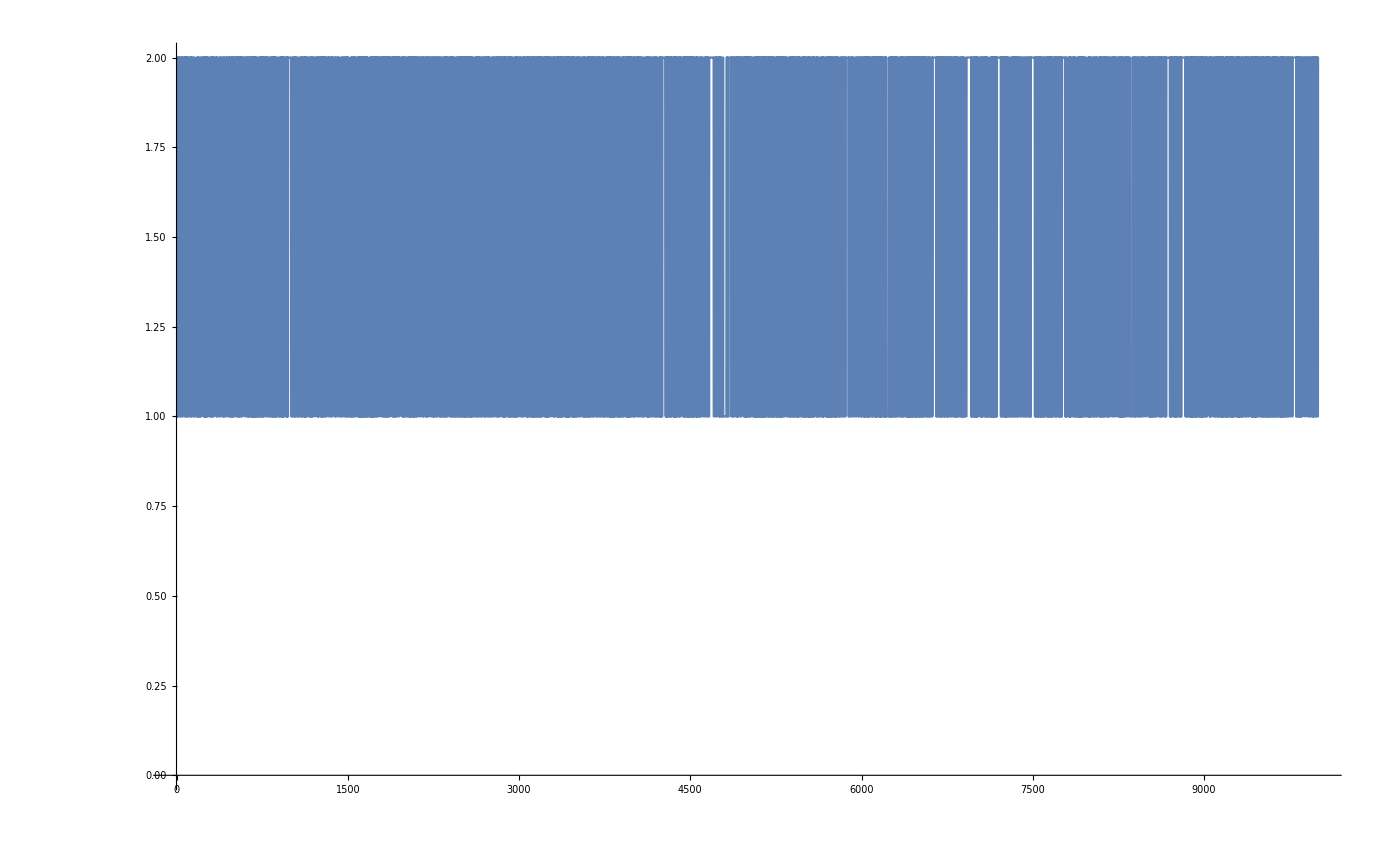

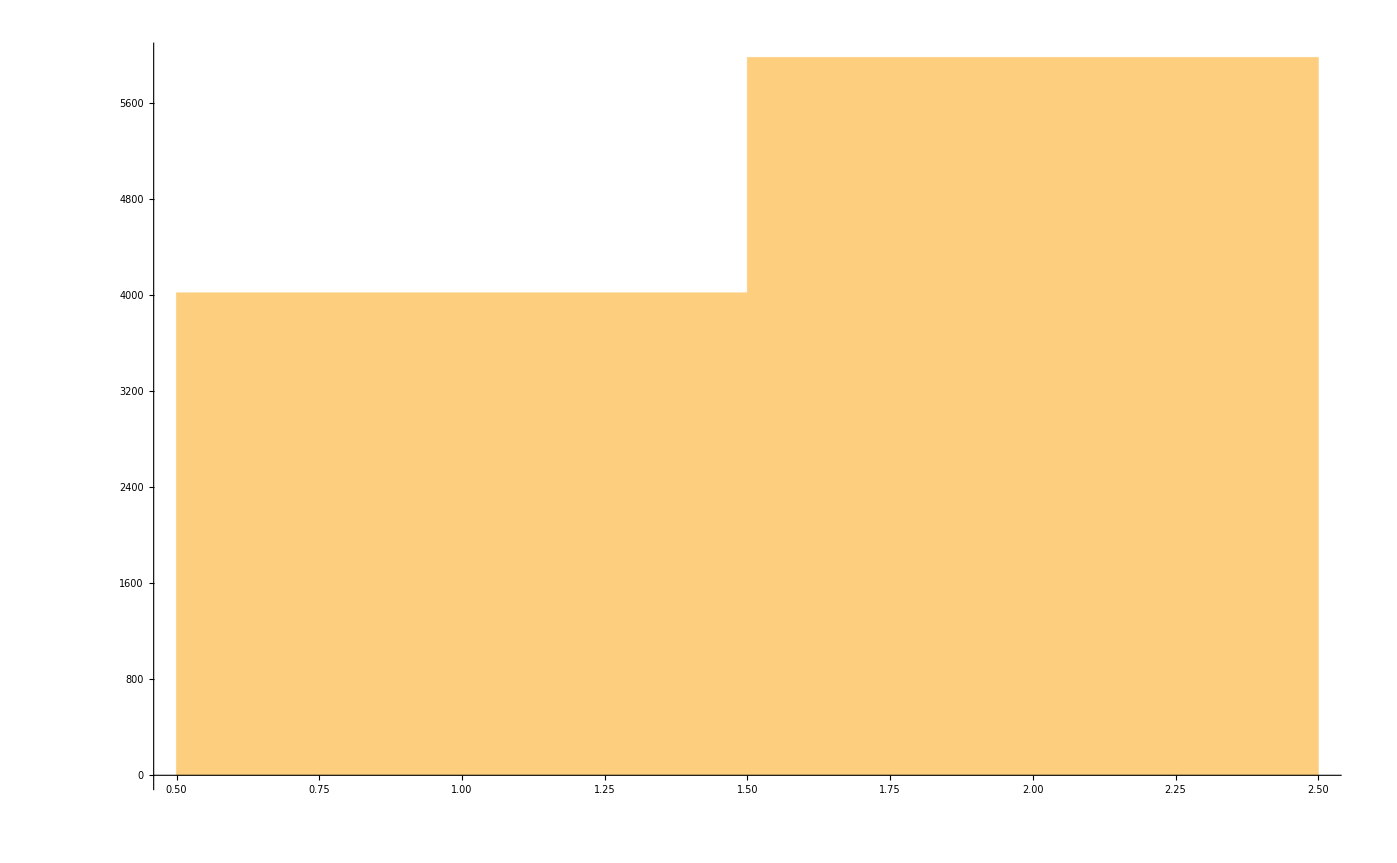

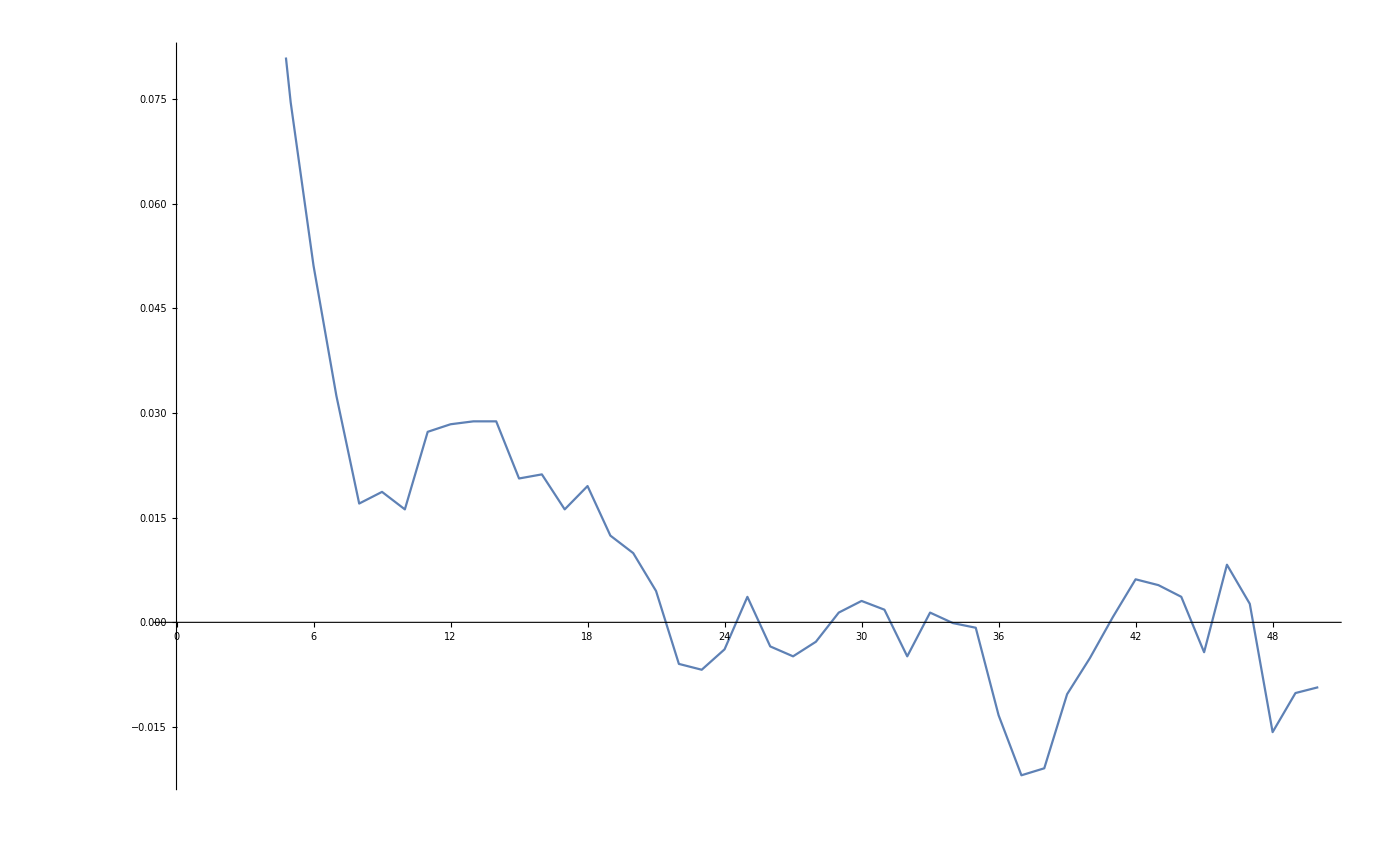

```mathematica
PP//MatrixForm
bincommchan=DiscreteMarkovProcess[{1,0},PP];
data=RandomFunction[bincommchan,{0,nn}]
datan=(data//Normal)[[1]];
Dimensions[datan]
ListPlot[datan,Joined->True]
Histogram[data]
Do[corr[tau]=Correlation[Table[datan[[t,2]],{t,1,nn-tauM}],
                                                  Table[datan[[t+tau,2]],{t,1,nn-tauM}]],
   {tau,0,tauM}];
AC=Table[{tau,corr[tau]},{tau,0,tauM}];
ListPlot[AC,Joined->True]
```

```mathematica
5896/nn//N
QQ[[1,1]]
```

0.5896

0.588235

```mathematica
PP//MatrixForm
QQ//MatrixForm
```

(0.8 | 0.2
0.4 | 0.6)

(0.666667 | 0.333333
0.666667 | 0.333333)